```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
list=FileNames["./output/ctags*.out","",2];
```

```mathematica
data=Import["./output/ctags"<>ToString[100]<>".out","Table"];
```

```mathematica
Sort[DeleteDuplicates[Flatten@data]] //Last
```

176

```mathematica
M=140 50
```

7000

```mathematica
hue[x_]:=If[x==0,{0,0,0},{Piecewise[{{2-6x, 1/6<x≤2/6}, {0, 2/6<x≤4/6}, {6x-4, 4/6<x≤5/6}, {1, True}}],Piecewise[{{6x, 0/6<x≤1/6}, {1, 1/6<x≤3/6}, {4-6x, 3/6<x≤4/6}, {0, True}}],Piecewise[{{0, 0/6<x≤2/6}, {6x-2, 2/6<x≤3/6}, {6-6x, 5/6<x≤6/6}, {1, True}}]}];
```

```mathematica
permute=RandomSample[Range[M]];
```

```mathematica
changes=Table[i-> permute[[i]],{i,1,M}];
```

```mathematica
permute2=RandomSample[Range[M]];
changes2=Table[i-> permute2[[i]],{i,1,M}];
```

```mathematica
Clear[ColorsReplace]
```

```mathematica
ColorsReplace[x_]:=(ColorsReplace[x]={1,1,1}(0.6(x/.changes)/M+If[x==0,0,0.4])-{0.3,0.3,0.3}hue[(x/.changes2)/M])
```

```mathematica
ColorsReplace[1]
```

{0.433257,0.139943,0.133257}

```mathematica
data=Import["./output/ctags"<>ToString[100#]<>".out","Table"]&/@Range[12];
```

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

```mathematica
ImageAssemble@Partition[Map[Image[Map[ColorsReplace,#,{2}]ᵀ]&,data],3]
```

-Graphics-

```mathematica
indexes=Import["./output/ctags"<>ToString[1200]<>".out","Table"];
```

```mathematica
fibersI=Import["./output/fib.out","Table"];
```

```mathematica
Image[Map[ColorsReplace,indexes[[;;,;;]],{2}]ᵀ+0.1fibersIᵀ]
```

-Graphics-

```mathematica
a12=ImageAssemble[{ImagePad[ImageResize[#,Last@ImageDimensions[a1]],{{0,0},{10,0}}]&/@{a1,a2,a3}}ᵀ]
```

-Graphics-

```mathematica
CellDetect[arr_,n_]:=Map[If[#==n,1,0]&,arr,{2}];
```

```mathematica
CellSizeX[arr_]:=Module[{c=Total[arr]},Mean[c]];
```

```mathematica
cellNs=(Sort@DeleteDuplicates@Flatten@indexes)[[2;;100]]; cellN=Max[cellNs];
cellMasks=CellDetect[indexes,#]&/@cellNs;
cellImgs=ImageCrop[Image[1-cellMasks[[#]]]]&/@cellNs;
cellRSizes=ImageDimensions[cellImgs[[#]]]&/@cellNs;
```

```mathematica
cellImgs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cellSizes=Module[{dat=ImageData[cellImgs[[#]]]},{CellSizeX[datᵀ],CellSizeX[dat]}]&/@cellNs;
```

```mathematica
cellVolumes=Total[Flatten@cellMasks[[#]]]&/@cellNs;
```

```mathematica
{Mean[x],StandardDeviation[x],StandardDeviation[x]/Mean[x]}/.x->(cellRSizes[[;;,2]]/cellSizes[[;;,1]])
```

{4.83591,2.2757,0.470584}

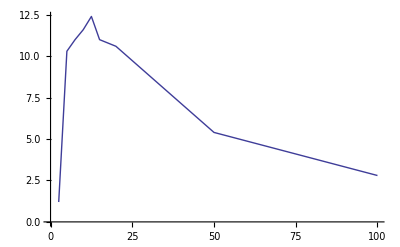

```mathematica
{{2.5,1.2},{5,10.3},{7.5,11},{10,11.6},{12.5,12.4},{15,11},{20,10.6},{50,5.4},{100,2.8}}//ListLinePlot
```

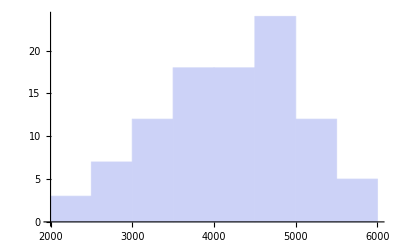

```mathematica
2.5^2 cellVolumes //Histogram
```

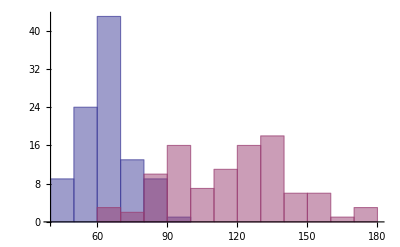

```mathematica
Histogram[2.5{cellRSizes[[;;,1]],cellRSizes[[;;,2]]},10]
```

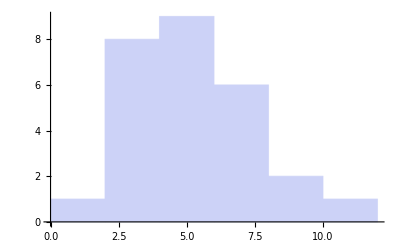

```mathematica
Histogram[cellRSizes[[;;,1]]/cellSizes[[;;,2]] ,5]
```

```mathematica
indexes=Import["./output/ctags1200.out","Table"]ᵀ;
```

```mathematica
conts=Import["./output/contactM1201.out","Table"]ᵀ;
```

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
cells=Map[ColorsReplace,indexes,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
outerConts=ArrayPad[Table[If[conts⟦i,j⟧==1,1-BorderQ[indexes,i,j],0],{i,2,Lx-1},{j,2,Ly-1}],1];
```

```mathematica
Image[ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]]
```

-Graphics-

```mathematica
{Lx,Ly}
```

{1980,2060}

```mathematica
data=Import["./output/ctags1200.out","Table"]ᵀ;
```

```mathematica
contsI=Import["./output/contactM1201.out","Table"]ᵀ;
```

```mathematica
σ=4; proc=0.3;Counts[arr_]:=Module[{uni=DeleteDuplicates[arr]},{Map[Count[arr,#]&,uni],uni}ᵀ];
Replacement[arr_]:=Module[{c=Counts[Flatten@arr]},Sort[c,#1[[1]]>#2[[1]]&]ᵀ[[2,1]]];
RepConts[arr_]:=If[Total[Flatten@arr]<(σ+1),0,1];
ContsW[arr_]:=Total[Flatten@arr]/(σ+1)^2;
```

```mathematica
If[σ==0,
indexes=data;
conts=contsI,
indexes=Table[Replacement[data[[i;;i+σ,j;;j+σ]]],{i,1,Dimensions[data][[1]]-σ,σ+1},{j,1,Dimensions[data][[2]]-σ,σ+1}];
conts=Table[RepConts[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
contsW=Table[ContsW[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
fibers=Table[RepConts[fibersI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[fibersI][[1]]-σ,σ+1},{j,1,Dimensions[fibersI][[2]]-σ,σ+1}]
];
```

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
cells=Map[ColorsReplace,indexes,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
outerConts=ArrayPad[Table[If[conts⟦i,j⟧==1,1-BorderQ[indexes,i,j],0],{i,2,Lx-1},{j,2,Ly-1}],1];
```

```mathematica
Image[ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]]
```

-Graphics-

```mathematica
vertBord=ArrayPad[Map[If[#≠0,1,0]&,indexes[[2;;]]-indexes[[;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[2;;]],{2}] Map[If[#≠0,1,0]&,indexes[[;;-2]],{2}],{{1,0},{0,0}}]ᵀ;vert=ArrayPad[Map[If[#==0,1,0]&,indexes[[2;;]]-indexes[[;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[2;;]],{2}],{{1,0},{0,0}}]ᵀ+2 vertBord;
```

```mathematica
horBord=ArrayPad[Map[If[#≠0,1,0]&,indexes[[;;,2;;]]-indexes[[;;, ;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[;;,2;;]],{2}] Map[If[#≠0,1,0]&,indexes[[;;, ;;-2]],{2}],{{0,0},{1,0}}]ᵀ;
hor=ArrayPad[Map[If[#==0,1,0]&,indexes[[;;,2;;]]-indexes[[;;, ;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[;;,2;;]],{2}],{{0,0},{1,0}}]ᵀ+2 horBord;
```

```mathematica
Image[((vertᵀ)~Join~(horᵀ))/2]
```

-Graphics-

```mathematica
Subscript[c, in]=1; Subscript[c, L]=0.22; Subscript[c, T]=0.06;
```

```mathematica
Dimensions[contsW]
```

{396,412}

```mathematica
Dimensions[vert ]
```

{412,396}

```mathematica
vertR=(vert/.{2->Subscript[c, T],1->Subscript[c, in]})+vertBord contsWᵀ (Subscript[c, L]-Subscript[c, T]);
horR=(hor/.{2->Subscript[c, T],1->Subscript[c, in]})+horBord contsWᵀ(Subscript[c, L]-Subscript[c, T]);
```

```mathematica
DeleteDuplicates[Flatten@(Map[If[#≠0,1,0]&,horBord contsWᵀ ,{2}]hor)]//N
```

{0.,2.}

```mathematica
TotalPar[arr_]:=If[Total[arr]==0,0,Times@@arr/Total[arr]];
FindRVert[arr_]:=Module[{c=Map[TotalPar,arr]},Total[c]]
```

```mathematica
(*horRsmall=ArrayPad[Table[FindRVert[horR⟦i;;i+dl-1,j-l1;;j+l2⟧],{i,1+l1,Ly-dl+1,dl},{j,1+l1,Lx-l2,dl}],{{1,0},{0,0}}];
vertRsmall=ArrayPad[Table[FindRVert[vertR⟦i-l1;;i+l2,j;;j+dl-1⟧ᵀ],{i,1+l1,Ly-l2,dl},{j,1+l1,Lx-dl+1,dl}],{{0,1},{1,0}}];
indexesRsmall=Table[indexes⟦j,i⟧,{i,1+l1,Ly,dl},{j,1+l1,Lx,dl}];*)
```

```mathematica
IfAny[arr_]:=If[Total[Flatten@arr]≠0,1,0];
IfHalf[arr_]:=If[Total[Flatten@arr]≥dl^2/2,1,0];
IfLine[arr_]:=If[Total[Flatten@arr]≥dl,1,0];
```

```mathematica
(*contsRsmall=ArrayPad[Table[IfLine@outerConts⟦j-l1;;j+l2,i-l1;;i+l2⟧,{i,1+l1,Ly-l2,dl},{j,1+l1,Lx-l2,dl}],{{1,0},{0,0}}];*)
```

```mathematica
niceCells=(ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]);
```

```mathematica
leaveX=32 12; leaveY = 32 12; shiftx=-5;shifty=-5;
 cutX=Floor[(First@Dimensions[indexes]-leaveX)/2]+1;
cutY=Floor[(Last@Dimensions[indexes]-leaveY)/2]+1;
halfX=If[OddQ[First@Dimensions[indexes]-leaveX],1,0];
halfY=If[OddQ[Last@Dimensions[indexes]-leaveY],1,0];
Image[niceCells⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧]
```

-Graphics-

```mathematica
ind=indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧;
```

```mathematica
endsCut=conts⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
```

```mathematica
indCut=Map[If[#≠0,1,0]&,ind,{2}]ᵀ;
```

```mathematica
vertCut=vertRᵀ⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
horCut=horRᵀ⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
```

```mathematica
Dimensions@(indCut)
```

{384,384}

```mathematica
Dimensions@(vertCut)
```

{384,384}

```mathematica
Gather[Flatten@endsCut][[;;,1]]
```

{0,1}

```mathematica
Gather[Flatten@indCut][[;;,1]]
```

{0,1}

```mathematica
filename="./maps/cells.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@indCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(indCutᵀ),"Integer8"];Close[filename]
```

./maps/cells.bin

```mathematica
filename="./maps/dx.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@vertCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(vertCutᵀ),"Real64"];Close[filename]
```

./maps/dx.bin

```mathematica
filename="./maps/dy.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@horCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(horCutᵀ),"Real64"]; Close[filename]
```

./maps/dy.bin

```mathematica
filename="./maps/na.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@endsCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(endsCutᵀ),"Integer8"]; Close[filename]
```

./maps/na.bin

```mathematica
files=FileNames["../nrvm-discrete/test/*.png"];
filesT=FileNames["../nrvm-discrete/testT/*.png"];
```

```mathematica
mov=Import/@files;
movT=Import/@filesT;
```

```mathematica
dat=ImageData/@mov;
datT=ImageData/@movT;
```

```mathematica
Manipulate[ListPlot[{dat[[t,100,;;]],datT[[t,;;,100]]},PlotRange->{0,0.6}],{t,1,Min[Length@mov,Length@movT],1}]
```

Part::partd: Part specification {{0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 462 »}, {0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 462 »}, « 48 », « 462 »} is longer than depth of object.

ListPlot::lpn: {{{0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 462 »}, {0, 0, 0, 0, 0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 462 »}, « 48 », « 462 »} ⟦ 1, 100, 1 ;; All ⟧, {0.105882, « 49 », « 334 »}} is not a list of numbers or pairs of numbers.

```mathematica
FindFront[arr_]:=Module[{c=Reverse@Map[If[#>0.3,1,0]&,arr]},Length@c-Position[c,1][[1,1]]]
```

```mathematica
front=FindFront[#[[150,;;]]]&/@dat;
frontT=FindFront[#[[;;,200]]]&/@datT;
```

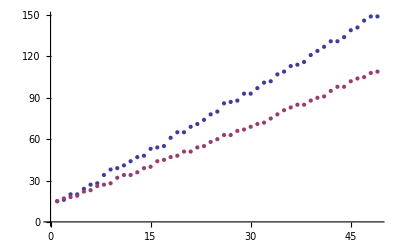

```mathematica
ListPlot[{front[[;;Length@frontT]],frontT}]
```

```mathematica
Export["./imgs/gif.gif",movT[[;;350]]]
```

./imgs/gif8T.gif

```mathematica
t1=10;t2=47; t3= t2;
vels={LinearModelFit[front[[t1;;t2]],x,x][[1,2,2]],LinearModelFit[frontT[[t1;;t3]],x,x][[1,2,2]]}(12.5 10^-4)/(50 10^-9 10^4)
```

{7.17693,4.99097}

```mathematica
vels[[1]]/vels[[2]]
```

1.43798

```mathematica
Image[Map[1-#&,borders,{2}]]
```

Image::imgarray: The specified argument borders should be an array of rank 2 or 3 with machine-sized numbers.

Image[borders]

```mathematica
σ=4; proc=0.3;Counts[arr_]:=Module[{uni=DeleteDuplicates[arr]},{Map[Count[arr,#]&,uni],uni}ᵀ];
Replacement[arr_]:=Module[{c=Counts[Flatten@arr]},Sort[c,#1[[1]]>#2[[1]]&]ᵀ[[2,1]]];
RepConts[arr_]:=If[Total[Flatten@arr]<(σ+1)^2 proc,0,1];
```

```mathematica
If[σ==0,
indexes=data;
conts=contsI,
indexes=Table[Replacement[data[[i;;i+σ,j;;j+σ]]],{i,1,Dimensions[data][[1]]-σ,σ+1},{j,1,Dimensions[data][[2]]-σ,σ+1}];
conts=Table[RepConts[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
fibers=Table[RepConts[fibersI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[fibersI][[1]]-σ,σ+1},{j,1,Dimensions[fibersI][[2]]-σ,σ+1}]
];
```